1

1.7×10^-11

0.00729753

0.1101

0.09207

6.×10^-6

0.000183399

0.000022

0.000250729

5.×10^-7

0.134976

1.8×10^-7

0.13957

0.00006

0.957764

0.00023

0.775105

0.00013

0.78279

0.000016

1.01946

0.00013

0.0086398

0.0008

0.14946

0.000013

0.00425694

49/50

0.000016

0.493669

-Graphics3D-

0.01

0.70957

0.01

0.643418

0.5

0.718387

0.1

0.0585741

0.02

0.816512

0.236523

0.381327

0.708353

0.140305

0.0415386

-0.221314

0.0901926

0.0993857

-0.00919308

21.1865

0.0948774

0.00770907

-0.0000466528

5.71854×10^-7

5.49419×10^-7

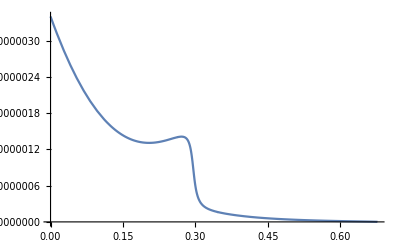

0.005

3.17×10^-6

6.8×10^-7

0.025

2.57×10^-6

3.7×10^-7

0.05

2.6×10^-6

3.3×10^-7

0.075

1.87×10^-6

2.6×10^-7

0.105

1.76×10^-6

2.4×10^-7

0.14

1.63×10^-6

2.2×10^-7

0.18

1.76×10^-6

2.2×10^-7

0.225

1.97×10^-6

2.4×10^-7

0.265

2.×10^-6

3.2×10^-7

0.295

1.07×10^-6

2.8×10^-7

0.335

3.4×10^-7

9.×10^-8

0.39

1.2×10^-7

4.×10^-8

0.53

6.×10^-8

2.×10^-8

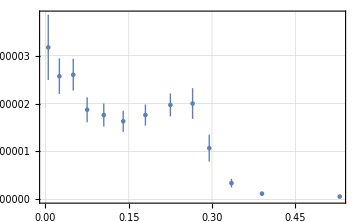

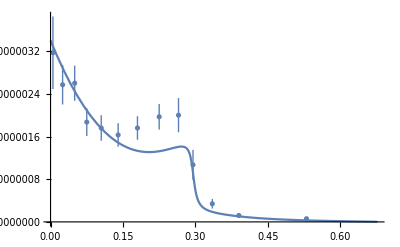

5.49419×10^-7

0.00299576

```mathematica
VarianceInput = 1
Δα=0.000000017*10^(-3)
α=7.297525664*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δα
fK =110.10*10^(-3)
fπ =92.07*10^(-3)
ΔΓtotal=0.006*10^(-3)
Γtotal=0.188*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔΓtotal
ΔBR=0.22*10^(-4)
BR=2.56*10^(-4)+VarianceInput*RandomReal[{-1,1}]*ΔBR
Δmπ=0.0005*10^(-3)
mπ=134.9768*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δmπ
ΔmπA=0.00018*10^(-3)
mπA=139.57039*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔmπA
ΔMηPrime=0.06*10^(-3)
MηPrime = 957.78*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔMηPrime
Δmρ=0.23*10^(-3)
mρ=775.26*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δmρ
Δmω=0.13*10^(-3)
mω=782.66*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δmω
Δmϕ=0.016*10^(-3)
mϕ=1019.461*10^(-3)+VarianceInput*RandomReal[{-1,1}]*Δmϕ
ΔΓω =0.13*10^(-3)
Γω = 8.68*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔΓω
ΔΓρ=0.8*10^(-3)
Γρ = 149.1*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔΓρ
ΔΓϕ=0.013*10^(-3)
Γϕ = 4.249*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔΓϕ
maZero = 980*10^(-3)
ΔmKP=0.016*10^(-3)
mKP=493.677*10^(-3)+VarianceInput*RandomReal[{-1,1}]*ΔmKP
ΓρEff[t_] :=Γρ*((-4 mπA^2+t)/(-4 mπA^2+mρ^2))^(3/2) *HeavisideTheta[-4 mπA^2+t]
m232MAX[m132_] := ((MηPrime^2+mπ^2)^2)/(4 m132)-(-(-m132+MηPrime^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
m232MIN[m132_] := ((MηPrime^2+mπ^2)^2)/(4 m132)-((-m132+MηPrime^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
Constraint[m132_, m232_]:=HeavisideTheta[m232MAX[m132]-m232]*HeavisideTheta[m232-m232MIN[m132]]
Plot3D[Constraint[m132, m232], {m132, mπ^2, MηPrime^2},{m232, mπ^2, MηPrime^2}, PlotRange->All]
Δg=0.01
g = 0.70+VarianceInput*RandomReal[{-1,1}]*Δg
ΔzSmBm=0.01
zSmBm = 0.65+VarianceInput*RandomReal[{-1,1}]*ΔzSmBm
ΔϕP=0.5
ϕP = (41.4 +VarianceInput*RandomReal[{-1,1}]*ΔϕP)Degree
ΔϕV=0.1
ϕV =(3.3 +VarianceInput*RandomReal[{-1,1}]*ΔϕV)Degree
ΔzNS=0.02
zNS = 0.83+VarianceInput*RandomReal[{-1,1}]*ΔzNS
gρπγ = g/3
gρηPγ = g*zNS*Sin[ϕP]

gωπγ = g*Cos[ϕV]
gωηPγ =g/3*(zNS*Sin[ϕP]*Cos[ϕV]+2*zSmBm*Cos[ϕP]*Sin[ϕV])
gϕπγ = g*Sin[ϕV]
gϕηPγ =g/3*(zNS*Sin[ϕP]*Sin[ϕV]-2*zSmBm*Cos[ϕP]*Cos[ϕV])
cρ = gρπγ*gρηPγ
cω = gωπγ*gωηPγ
cϕ = gϕπγ*gϕηPγ
Bq2Bq2p[m132_,m232_]:=1/8 (m132^2+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
Bq1Bq1[m132_,m232_]:=1/8 (m232^2+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
Bq2Bq1[m132_,m232_]:=1/8 (m132*m232+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
BWt[m132_,m232_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)]^2
BWu[m132_,m232_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)]^2
BWtu[m132_,m232_] :=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω))]
MatrixVMD[m132_,m232_] := (Bq2Bq2p[m132,m232]*BWt[m132,m232]+2*Bq2Bq1[m132,m232]*BWtu[m132,m232] +Bq2Bq1[m132,m232]*BWu[m132,m232])*Constraint[m132, m232]
βPlusπηP[s_]:=√(1-(MηPrime+mπ)^2/s)
βMinusπηP[s_]:=√(1-(MηPrime-mπ)^2/s)
βBarPlusπηP[s_]:=√(-1+(MηPrime+mπ)^2/s)
βBarMinusπηP[s_]:=√(-1+(-MηPrime+mπ)^2/s)
βK[s_]:=√(1-(4*mKP^2)/s)
βKbar[s_]:=√((4*mKP^2)/s-1)
θπηP[s_]:= HeavisideTheta[-(MηPrime+mπ)^2+s]
BarθπηP[s_]:= HeavisideTheta[(MηPrime+mπ)^2-s]*HeavisideTheta[-(-MηPrime+mπ)^2+s]
BarBarθπηP[s_]:= HeavisideTheta[(-MηPrime+mπ)^2-s]
θK[s_]:= HeavisideTheta[-4*mKP^2+s]
θKbar[s_]:= HeavisideTheta[4*mKP^2-s]
ga0KKbarSq=((-maZero^2+mKP^2)^2)/(2 fK^2)
ga0πηPSq=((-maZero^2+MηPrime^2)^2 Sin[ϕP]^2)/fπ^2
R1[s_]:=ga0KKbarSq/(16 π^2)*(2-Log[(1+βK[s])/(1-βK[s])] *βK[s]* θK[s]-2 ArcTan[1/βKbar[s]]* βKbar[s]* θKbar[s])
R2[s_]:=ga0πηPSq/(16 π^2)*(2-((MηPrime^2-mπ^2) *Log[MηPrime/mπ])/s-Log[(βMinusπηP[s]+βPlusπηP[s])/(βMinusπηP[s]-βPlusπηP[s])]* βMinusπηP[s]* βPlusπηP[s]* θπηP[s])
R3[s_]:=ga0πηPSq/(16 π^2)*(BarBarθπηP[s]*Log[(βBarMinusπηP[s]+βBarPlusπηP[s])/(-βBarMinusπηP[s]+βBarPlusπηP[s])]*βBarMinusπηP[s]*βBarPlusπηP[s]-2*ArcTan[βMinusπηP[s]/βBarPlusπηP[s]]*BarθπηP[s]*βBarPlusπηP[s]*βMinusπηP[s])
R[s_]:=R1[s]+R2[s]+R3[s]
ImaginaryPart[s_]:=-(ga0KKbarSq* βK[s]* θK[s])/(16 π)-(ga0πηPSq* βPlusπηP[s]* βMinusπηP[s]*θπηP[s])/(16 π)
Da0[s_]:=-maZero^2+s+R[s]-R[maZero^2]+I*ImaginaryPart[s]
ALSM[s_]:=1/(2*fK*fπ)*((-MηPrime^2+s)*((-maZero^2+mKP^2)/Da0[s])*Sin[ϕP]+1/6 ((5 MηPrime^2+mπ^2-3 s)*Sin[ϕP]+√2*(4 mKP^2+MηPrime^2+mπ^2-3 s)*Cos[ϕP]))
f[z_]:=1/4* HeavisideTheta[1/4-z] *(-ⅈ π+Log[(1+√(1-4 z))/(1-√(1-4 z))])^2-ArcSin[1/(2 √z)]^2 HeavisideTheta[-1/4+z]
L[z_]:=-1/(2 z)-(2 f[1/z])/z^2
Int1VMDLSM[m132_,m232_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2]*ALSM[-m132-m232+MηPrime^2+mπ^2]
Int2VMDLSM[m132_,m232_]:=-Conjugate[1/4 (-m132-m232+MηPrime^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)))]
Interference[m132_,m232_]:=2*Re[Int1VMDLSM[m132,m232]*Int2VMDLSM[m132,m232]]*Constraint[m132, m232]
LSM[m132_,m232_]:=((-m132-m232+MηPrime^2+mπ^2)^2*Abs[(α ALSM[-m132-m232+MηPrime^2+mπ^2]* L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2])/mKP^2]^2)/π^2*Constraint[m132, m232]
Integrand1 = NIntegrate[MatrixVMD[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2 = NIntegrate[Interference[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3 = NIntegrate[LSM[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Width = (1/2)*1/(256 MηPrime^3 π^3)*(Integrand1+Integrand2+Integrand3)
γγSpectrum[m122_] := NIntegrate[(1/2)*1/(256 MηPrime^3 π^3)*(MatrixVMD[m132,MηPrime^2+mπ^2 - m132 - m122]+Interference[m132,MηPrime^2+mπ^2 - m132 - m122]+LSM[m132,MηPrime^2+mπ^2 - m132 - m122])*Constraint[m132, MηPrime^2+mπ^2 - m132 - m122], {m132, mπ^2,MηPrime^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
pTheory= Plot[γγSpectrum[m122],{m122, 0, (MηPrime-mπ)^2} , MaxRecursion->5]
p1 = (0.0 + 0.01)/2
v1 = 3.17*10^(-6)
u1 = (0.44 + 0.24)*10^(-6)
p2 = (0.01 + 0.04)/2
v2 = 2.57*10^(-6)
u2 = (0.18+0.19)*10^(-6)
p3 = (0.04 + 0.06)/2
v3 = 2.60*10^(-6)
u3 = (0.15 + 0.18)*10^(-6)
p4  = (0.06 + 0.09)/2
v4 = 1.87*10^(-6)
u4 = (0.12 +0.14)*10^(-6)
p5 = (0.09 + 0.12)/2
v5 = 1.76*10^(-6)
u5 = (0.11 + 0.13)*10^(-6)
p6 = (0.12 + 0.16)/2
v6 = 1.63*10^(-6)
u6 = (0.10 + 0.12)*10^(-6)
p7 = (0.16 + 0.20)/2
v7 = 1.76*10^(-6)
u7 = (0.09 + 0.13)*10^(-6)
p8 = (0.20 + 0.25)/2
v8 = 1.97*10^(-6)
u8 = (0.10 + 0.14)*10^(-6)
p9 = (0.25+0.28)/2
v9 = 2.00*10^(-6)
u9 = (0.17 + 0.15)*10^(-6)
p10 = (0.28 + 0.31)/2
v10 = 1.07*10^(-6)
u10 = (0.20 + 0.08)*10^(-6)
p11 = (0.31 + 0.36)/2
v11 = 0.34*10^(-6)
u11  = (0.06 + 0.03)*10^(-6)
p12 = (0.36 + 0.42)/2
v12 = 0.12 *10^(-6)
u12 = (0.03 + 0.01)*10^(-6)
p13 = (0.42 + 0.64)/2
v13 = 0.06*10^(-6)
u13  = (0.01 + 0.01)*10^(-6)
pExp=ListPlot[{{Around[p1,0],Around[v1,u1]},{Around[p2,0],Around[v2,u2]},{Around[p3,0],Around[v3,u3]},{Around[p4,0],Around[v4,u4]},{Around[p5,0],Around[v5,u5]} ,{Around[p6,0],Around[v6,u6]},{Around[p7,0],Around[v7,u7]},{Around[p8,0],Around[v8,u8]},{Around[p9,0],Around[v9,u9]}
,{Around[p10,0],Around[v10,u10]},{Around[p11,0],Around[v11,u11]},{Around[p12,0],Around[v12,u12]}
,{Around[p13,0],Around[v13,u13]}},Sequence[PlotTheme->"Detailed",ImageSize->Medium]]
Show[pTheory, pExp, PlotRange->All]
Width
BranchingTheory=Width/Γtotal
```

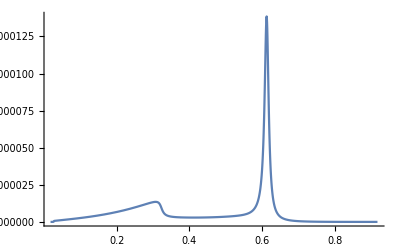

```mathematica
πγ1[m132_] := NIntegrate[MatrixVMD[m132,m232], {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγ2[m132_] := NIntegrate[Interference[m132,m232],  {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγ3[m132_] := NIntegrate[LSM[m132,m232],  {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrum[m132_]  := (1/2)*1/(256 MηPrime^3 π^3)*(πγ1[m132]+πγ2[m132]+πγ3[m132])
πγSpectrumPlot= Plot[πγSpectrum[m132],{m132, (mπ)^2, (MηPrime)^2} , MaxRecursion->5, PlotRange->All]
```

```mathematica
(*Result 1*)
(*5.057950002425554*^-7*)
(*0.0027400163660190294*)
(*Result 2*)
(*5.302875913041425*^-7*)
(*0.0028036369138169084*)
(*Result 3*)
(*5.441057053056234*^-7*)
(*0.0028896887525844506*)
(*Result 4*)
(*5.246768733086007*^-7*)
(*0.002731825645273944*)
(*Result 5*)
(*5.614774208346448*^-7*)
(*0.0029268495906724715*)
(*Result 6*)
(*5.169487998099765*^-7*)
(*0.0027055852379944826*)
(*Result 7*)
(*5.37368203820295*^-7*)
(*0.002850770629318911*)
(*Result 8*)
(*5.400673061631221*^-7*)
(*0.0029661711231478032*)
(*Result 9*)
(*5.291097153375589*^-7*)
(*0.0027306632864117146*)
(*Result 10*)
(*5.364936753444081*^-7*)
(*0.0027881608177311454*)
```

```mathematica
EngineeringForm[Mean[{5.057950002425554*^-7,5.302875913041425*^-7,5.441057053056234*^-7,5.246768733086007*^-7,5.614774208346448*^-7,5.169487998099765*^-7,5.37368203820295*^-7,5.400673061631221*^-7,5.291097153375589*^-7,5.364936753444081*^-7}]]
```

532.633×10^-9

```mathematica
EngineeringForm[(Variance[{5.057950002425554*^-7,5.302875913041425*^-7,5.441057053056234*^-7,5.246768733086007*^-7,5.614774208346448*^-7,5.169487998099765*^-7,5.37368203820295*^-7,5.400673061631221*^-7,5.291097153375589*^-7,5.364936753444081*^-7}])^(1/2)]
```

15.2887×10^-9

```mathematica
EngineeringForm[Mean[{0.0027400163660190294,0.0028036369138169084,0.0028896887525844506,0.002731825645273944,0.0029268495906724715,0.0027055852379944826,0.002850770629318911,0.0029661711231478032,0.0027306632864117146,0.0027881608177311454}]]
```

2.81334×10^-3

```mathematica
EngineeringForm[(Variance[{0.0027400163660190294,0.0028036369138169084,0.0028896887525844506,0.002731825645273944,0.0029268495906724715,0.0027055852379944826,0.002850770629318911,0.0029661711231478032,0.0027306632864117146,0.0027881608177311454}])^(1/2)]
```

91.0846×10^-6

```mathematica
(*VMD-LσM interference is destructive, around -(0.5 - 0.7) %*)
```

```mathematica
Integrand2/Integrand1
```

-0.00616623

```mathematica
EngineeringForm[BranchingTheory]
```

2.80364×10^-3

```mathematica
(*Minimize χ^2 = ∑_(i=1)^N (Subscript[Theory, i]- Subscript[Experiment, i])^2/Subscript[σ, i]^2*)
```

```mathematica
BWtDARK[m132_,m232_,cB_,ΓB_,mB_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+cB/(- m132+mB^2-ⅈ mB* ΓB)]^2
BWuDARK[m132_,m232_,cB_,ΓB_,mB_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+cB/(-m232+mB^2-ⅈ* mB* ΓB)]^2
BWtuDARK[m132_,m232_,cB_,ΓB_,mB_]:=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+cB/(-m132+mB^2-ⅈ *mB* ΓB))*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω)+cB/(-m232+mB^2+ⅈ *mB* ΓB))]
MatrixVMDDARK[m132_,m232_,cB_,ΓB_,mB_] := (Bq2Bq2p[m132,m232]*BWtDARK[m132,m232,cB,ΓB,mB]+2*Bq2Bq1[m132,m232]*BWtuDARK[m132,m232,cB,ΓB,mB] +Bq2Bq1[m132,m232]*BWuDARK[m132,m232,cB,ΓB,mB])*Constraint[m132, m232]
Int1VMDLSMDARK[m132_,m232_,cB_,ΓB_,mB_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2]*ALSM[-m132-m232+MηPrime^2+mπ^2]
Int2VMDLSMDARK[m132_,m232_,cB_,ΓB_,mB_]:=-Conjugate[1/4 (-m132-m232+MηPrime^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+cB/(-m132+mB^2-ⅈ *mB* ΓB))+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+cB/(-m232+mB^2-ⅈ *mB* ΓB)))]
InterferenceDARK[m132_,m232_,cB_,ΓB_,mB_]:=2*Re[Int1VMDLSMDARK[m132,m232,cB,ΓB,mB]*Int2VMDLSMDARK[m132,m232,cB,ΓB,mB]]*Constraint[m132, m232]
γγSpectrumDARK[m122_,cB_,ΓB_,mB_] := NIntegrate[(1/2)*1/(256 MηPrime^3 π^3)*(MatrixVMDDARK[m132,MηPrime^2+mπ^2 - m132 - m122,cB,ΓB,mB]+InterferenceDARK[m132,MηPrime^2+mπ^2 - m132 - m122,cB,ΓB,mB]+LSM[m132,MηPrime^2+mπ^2 - m132 - m122])*Constraint[m132, MηPrime^2+mπ^2 - m132 - m122], {m132, mπ^2,MηPrime^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->50]
Loss[x_,Γ_,mB_]:=(γγSpectrumDARK[p1,x, Γ,mB]- v1)^2/u1^2+(γγSpectrumDARK[p2,x, Γ,mB]- v2)^2/u2^2+(γγSpectrumDARK[p3,x, Γ,mB]- v3)^2/u3^2+(γγSpectrumDARK[p4,x, Γ,mB]- v4)^2/u4^2+(γγSpectrumDARK[p5,x, Γ,mB]- v5)^2/u5^2+(γγSpectrumDARK[p6,x, Γ,mB]- v6)^2/u6^2+(γγSpectrumDARK[p7,x, Γ,mB]- v7)^2/u7^2
```

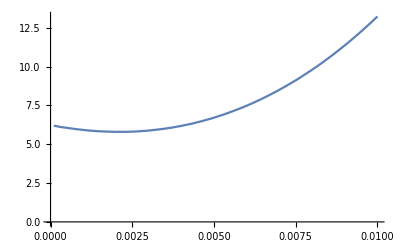

```mathematica
ListPlot[Table[{(0.01/100)*k,Loss[(0.01/100)*k,Γω/2,mω-Γω/2]},{k, 1, 100}],Joined->True]
```

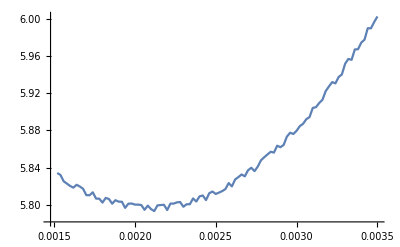

```mathematica
ListPlot[Table[{0.0015+(0.002/100)*k,Loss[0.0015+(0.002/100)*k,Γω/2,mω-Γω/2]},{k, 1, 100}],Joined->True]
```

```mathematica
(*Result 1 = 0.006*)
(*Result 2 = 0.003*)
(*Result 3 = 0.001*)
(*Result 4 = 0.004*)
(*Result 5 = 0.000*)
(*Result 6 = 0.004*)
(*Result 7 = 0.002*)
(*Result 8 = 0.002*)
(*Result 9 = 0.003*)
(*Result 10 = 0.002*)
```

```mathematica
Mean[{0.006,0.003,0.001,0.004,0.000,0.004,0.002,0.002,0.003,0.002}]
```

0.0027

```mathematica
(Variance[{0.006,0.003,0.001,0.004,0.000,0.004,0.002,0.002,0.003,0.002}])^(1/2)
```

0.00170294

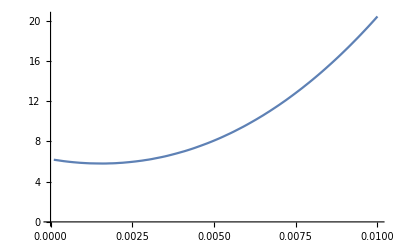

```mathematica
ListPlot[Table[{(0.01/100)*k,Loss[(0.01/100)*k,Γω/2,mω]},{k, 1, 100}],Joined->True]
```

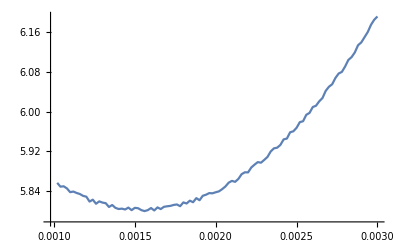

```mathematica
ListPlot[Table[{0.001+(0.002/100)*k,Loss[0.001+(0.002/100)*k,Γω/2,mω]},{k, 1, 100}],Joined->True]
```

```mathematica
(*Result 1 = 0.004*)
(*Result 2 = 0.002*)
(*Result 3 = 0.001*)
(*Result 4 = 0.003*)
(*Result 5 = 0.000*)
(*Result 6 = 0.003*)
(*Result 7 = 0.002*)
(*Result 8 = 0.001*)
(*Result 9 = 0.002*)
(*Result 10 = 0.002*)
```

```mathematica
Mean[{0.004,0.002,0.001,0.003,0.000,0.003,0.002,0.001,0.002,0.002}]
```

0.002

```mathematica
(Variance[{0.004,0.002,0.001,0.003,0.000,0.003,0.002,0.001,0.002,0.002}])^(1/2)
```

0.0011547

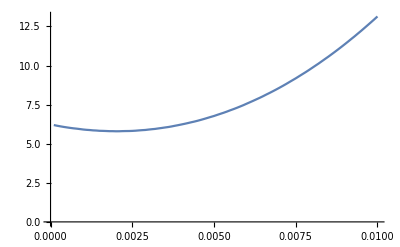

```mathematica
ListPlot[Table[{(0.01/100)*k,Loss[(0.01/100)*k,Γω,mω]},{k, 1, 100}],Joined->True]
```

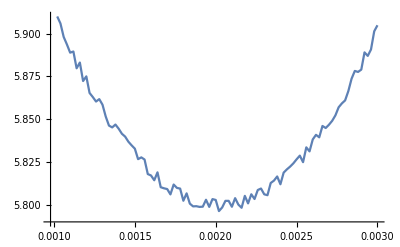

```mathematica
ListPlot[Table[{0.001+(0.002/100)*k,Loss[0.001+(0.002/100)*k,Γω,mω]},{k, 1, 100}],Joined->True]
```

```mathematica
(*Result 1 = 0.006*)
(*Result 2 = 0.003*)
(*Result 3 = 0.001*)
(*Result 4 = 0.004*)
(*Result 5 = 0.000*)
(*Result 6 = 0.004*)
(*Result 7 = 0.002*)
(*Result 8 = 0.002*)
(*Result 9 = 0.003*)
(*Result 10 = 0.002*)
Mean[{0.006,0.003,0.001,0.004,0.000,0.004,0.002,0.002,0.003,0.002}]
```

0.0027

```mathematica
(Variance[{0.006,0.003,0.001,0.004,0.000,0.004,0.002,0.002,0.003,0.002}])^(1/2)
```

0.00170294

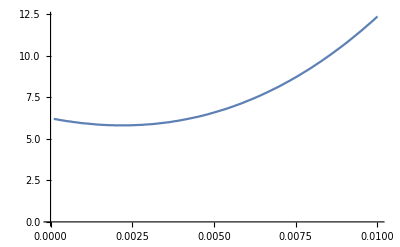

```mathematica
ListPlot[Table[{(0.01/100)*k,Loss[(0.01/100)*k,Γω/2,mω+Γω/2]},{k, 1, 100}],Joined->True]
```

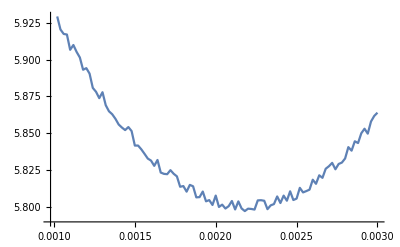

```mathematica
ListPlot[Table[{0.001+(0.002/100)*k,Loss[0.001+(0.002/100)*k,Γω/2,mω+Γω/2]},{k, 1, 100}],Joined->True]
```

```mathematica
(*Result 1 = 0.006*)
(*Result 2 = 0.003*)
(*Result 3 = 0.001*)
(*Result 4 = 0.004*)
(*Result 5 = 0.000*)
(*Result 6 = 0.005*)
(*Result 7 = 0.002*)
(*Result 8 = 0.002*)
(*Result 9 = 0.003*)
(*Result 10 = 0.002*)
```

```mathematica
Mean[{0.006,0.003,0.001,0.004,0.000,0.005,0.002,0.002,0.003,0.002}]
```

0.0028

```mathematica
(Variance[{0.006,0.003,0.001,0.004,0.000,0.005,0.002,0.002,0.003,0.002}])^(1/2)
```

0.00181353

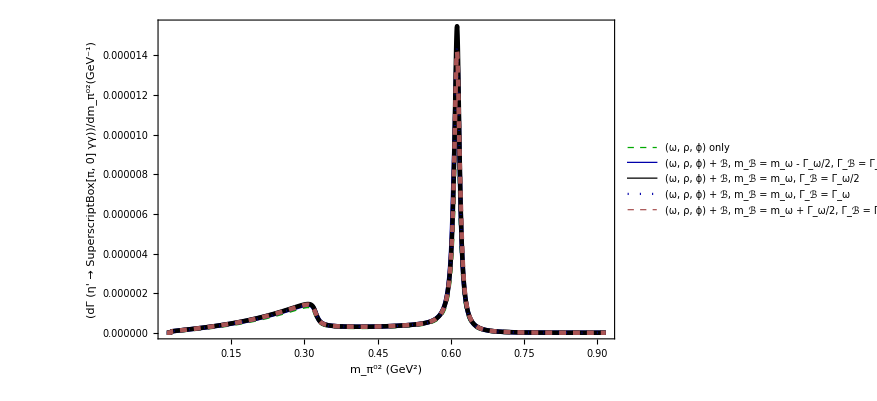

```mathematica
πγ1Dark[m132_,cB_,ΓB_,mB_]:= NIntegrate[MatrixVMDDARK[m132,m232,cB,ΓB,mB], {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγ2Dark[m132_,cB_,ΓB_,mB_] := NIntegrate[InterferenceDARK[m132,m232,cB,ΓB,mB],  {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγ3Dark[m132_,cB_,ΓB_,mB_] := NIntegrate[LSM[m132,m232],  {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrumDark[m132_,cB_,ΓB_,mB_]  := (1/2)*1/(256 MηPrime^3 π^3)*(πγ1Dark[m132,cB,ΓB,mB]+πγ2Dark[m132,cB,ΓB,mB]+πγ3Dark[m132,cB,ΓB,mB])
πγSpectrumPlotOverall = Plot[{{πγSpectrum[m132]},{πγSpectrumDark[m132,0.003,Γω/2,mω-Γω/2]},{πγSpectrumDark[m132,0.003,Γω/2,mω]},{πγSpectrumDark[m132,0.002,Γω,mω]},{πγSpectrumDark[m132,0.003,Γω/2,mω+Γω/2]}},{m132, (mπ)^2, (MηPrime)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Green], Thickness[0.005], Dashed],Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Black],Thickness[0.005]],Directive[Darker[Blue],Dotted],Directive[Darker[Pink], Dashed,Thickness[0.005]],Directive[Darker[Red], Thickness[0.005]]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"(ω, ρ, ϕ) only","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω - Γ_ω/2, Γ_ℬ = Γ_ω/2","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω, Γ_ℬ = Γ_ω/2","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω, Γ_ℬ = Γ_ω","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω + Γ_ω/2, Γ_ℬ = Γ_ω/2"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_(π^0)^2 (GeV^2)","(dΓ (η' →  SuperscriptBox[π, 0] γγ))/(dm_(π^0)^2)(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650]
```

```mathematica
Export["EtaPrimePiPi0GammaSpectrum.png",πγSpectrumPlotOverall]
```

EtaPrimePiPi0GammaSpectrum.png

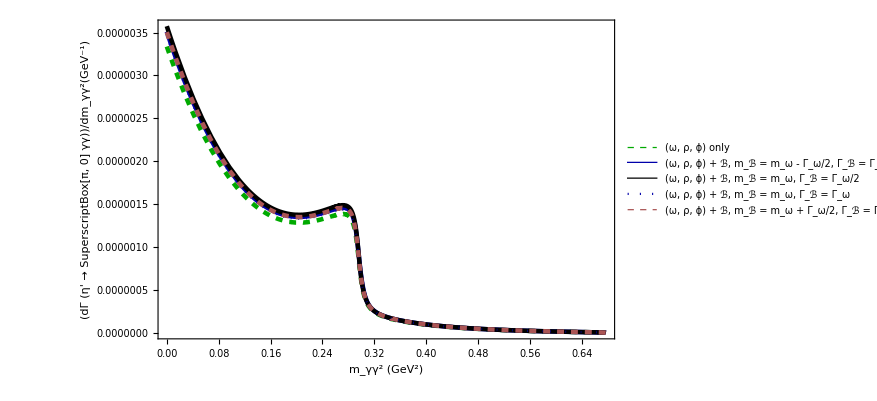

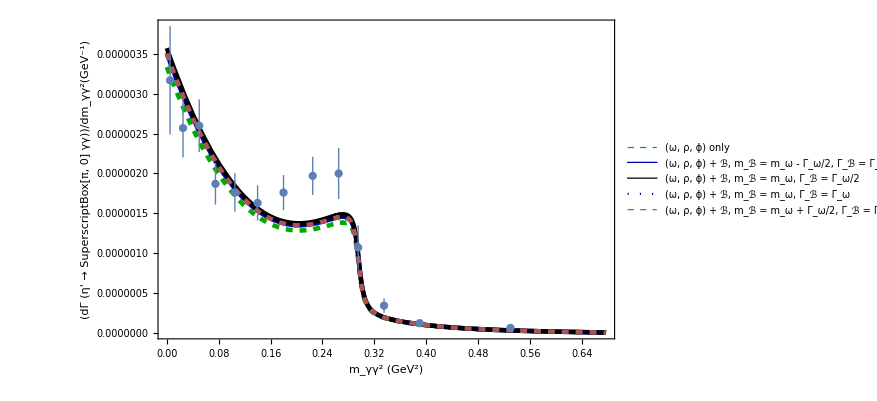

```mathematica
SummaryTheory = Plot[{{γγSpectrum[m122]},{γγSpectrumDARK[m122,0.003,Γω/2,mω-Γω/2]},{γγSpectrumDARK[m122,0.003,Γω/2,mω]},{γγSpectrumDARK[m122,0.002,Γω,mω]},{γγSpectrumDARK[m122,0.003,Γω/2,mω+Γω/2]}},{m122, 0, (MηPrime-mπ)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Green], Thickness[0.005], Dashed],Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Black],Thickness[0.005]],Directive[Darker[Blue],Dotted],Directive[Darker[Pink], Dashed,Thickness[0.005]],Directive[Darker[Red], Thickness[0.005]]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"(ω, ρ, ϕ) only","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω - Γ_ω/2, Γ_ℬ = Γ_ω/2","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω, Γ_ℬ = Γ_ω/2","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω, Γ_ℬ = Γ_ω","(ω, ρ, ϕ) + ℬ, m_ℬ = m_ω + Γ_ω/2, Γ_ℬ = Γ_ω/2"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_γγ^2 (GeV^2)","(dΓ (η' →  SuperscriptBox[π, 0] γγ))/dm_γγ^2(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650]
pFinal = Show[SummaryTheory, pExp]
```

```mathematica
Export["EtaPrimePi.png",pFinal]
```

EtaPrimePi.png

```mathematica
Integrand1Dark = NIntegrate[MatrixVMDDARK[m132,m232,0.002,Γω/2,mω-Γω/2], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2Dark = NIntegrate[InterferenceDARK[m132,m232,0.002,Γω/2,mω-Γω/2], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3Dark = NIntegrate[LSM[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 MηPrime^3 π^3)*(Integrand1Dark+Integrand2Dark+Integrand3Dark)
BranchingDark=WidthDark/Γtotal
```

0.00780111

-0.0000467109

5.72595×10^-7

5.56047×10^-7

0.00288978

```mathematica
(*Result 1*)
(*5.606735957204462*^-7*)
(*0.0030373072638757684*)
(*Result 2*)
(*5.576885731755183*^-7*)
(*0.0029485062366318864*)
(*Result 3*)
(*5.542778271920937*^-7*)
(*0.0029437118328768004*)
(*Result 4*)
(*5.613494548564527*^-7*)
(*0.002922768116435422*)
(*Result 5*)
(*5.633900403782555*^-7*)
(*0.0029368196260124643*)
(*Result 6*)
(*5.554205900832105*^-7*)
(*0.0029069373020301145*)
(*Result 7*)
(*5.573518576329362*^-7*)
(*0.002956785114267123*)
(*Result 8*)
(*5.582575383302127*^-7*)
(*0.003066075969750537*)
(*Result 9*)
(*5.582209087814859*^-7*)
(*0.002880902196899772*)
(*Result 10*)
(*5.560471963055117*^-7*)
(*0.0028897805823209794*)
```

```mathematica
Width=Mean[{5.606735957204462*^-7,5.576885731755183*^-7,5.542778271920937*^-7,5.613494548564527*^-7,5.633900403782555*^-7,5.554205900832105*^-7,5.573518576329362*^-7,5.582575383302127*^-7,5.582209087814859*^-7,5.560471963055117*^-7}]
```

5.58268×10^-7

```mathematica
ΔWidth = (Variance[{5.606735957204462*^-7,5.576885731755183*^-7,5.542778271920937*^-7,5.613494548564527*^-7,5.633900403782555*^-7,5.554205900832105*^-7,5.573518576329362*^-7,5.582575383302127*^-7,5.582209087814859*^-7,5.560471963055117*^-7}])^(1/2)
```

2.82166×10^-9

```mathematica
Branching=EngineeringForm[Mean[{0.0030373072638757684,0.0029485062366318864,0.0029437118328768004,0.002922768116435422,0.0029368196260124643,0.0029069373020301145,0.002956785114267123,0.003066075969750537,0.002880902196899772,0.0028897805823209794}]]
```

2.94896×10^-3

```mathematica
ΔBranching=EngineeringForm[(Variance[{0.0030373072638757684,0.0029485062366318864,0.0029437118328768004,0.002922768116435422,0.0029368196260124643,0.0029069373020301145,0.002956785114267123,0.003066075969750537,0.002880902196899772,0.0028897805823209794}])^(1/2)]
```

59.9479×10^-6

```mathematica
Integrand1Dark = NIntegrate[MatrixVMDDARK[m132,m232,0.002,Γω/2,mω], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2Dark = NIntegrate[InterferenceDARK[m132,m232,0.002,Γω/2,mω], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3Dark = NIntegrate[LSM[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 MηPrime^3 π^3)*(Integrand1Dark+Integrand2Dark+Integrand3Dark)
BranchingDark=WidthDark/Γtotal
```

0.00788376

-0.0000467132

5.73704×10^-7

5.61974×10^-7

0.00292058

```mathematica
(*Result 1*)
(*5.527959647724142*^-7*)
(*0.002994632192527268*)
(*Result 2*)
(*5.557306479801049*^-7*)
(*0.002938154662425043*)
(*Result 3*)
(*5.575652029523084*^-7*)
(*0.002961170743281857*)
(*Result 4*)
(*5.623240347989912*^-7*)
(*0.0029278424443043203*)
(*Result 5*)
(*5.612779988709637*^-7*)
(*0.0029258100509312233*)
(*Result 6*)
(*5.540295837940579*^-7*)
(*0.0028996571108713923*)
(*Result 7*)
(*5.630089701710128*^-7*)
(*0.002986796436402762*)
(*Result 8*)
(*5.534841448042516*^-7*)
(*0.0030398594188233642*)
(*Result 9*)
(*5.529100209013327*^-7*)
(*0.0028534934267861268*)
(*Result 10*)
(*5.619737415165631*^-7*)
(*0.002920580872988633*)

Width=Mean[{5.527959647724142*^-7,5.557306479801049*^-7,5.575652029523084*^-7,5.623240347989912*^-7,5.612779988709637*^-7,5.540295837940579*^-7,5.630089701710128*^-7,5.534841448042516*^-7,5.529100209013327*^-7,5.619737415165631*^-7}]
```

5.5751×10^-7

```mathematica
ΔWidth=(Variance[{5.527959647724142*^-7,5.557306479801049*^-7,5.575652029523084*^-7,5.623240347989912*^-7,5.612779988709637*^-7,5.540295837940579*^-7,5.630089701710128*^-7,5.534841448042516*^-7,5.529100209013327*^-7,5.619737415165631*^-7}])^(1/2)
```

4.24798×10^-9

```mathematica
Branching=EngineeringForm[Mean[{0.002994632192527268,0.002938154662425043,0.002961170743281857,0.0029278424443043203,0.0029258100509312233,0.0028996571108713923,0.002986796436402762,0.0030398594188233642,0.0028534934267861268,0.002920580872988633}]]
```

2.9448×10^-3

```mathematica
ΔBranching=EngineeringForm[(Variance[{0.002994632192527268,0.002938154662425043,0.002961170743281857,0.0029278424443043203,0.0029258100509312233,0.0028996571108713923,0.002986796436402762,0.0030398594188233642,0.0028534934267861268,0.002920580872988633}])^(1/2)]
```

52.9202×10^-6

```mathematica
Integrand1Dark = NIntegrate[MatrixVMDDARK[m132,m232,0.002,Γω,mω], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2Dark = NIntegrate[InterferenceDARK[m132,m232,0.002,Γω,mω], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3Dark = NIntegrate[LSM[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 MηPrime^3 π^3)*(Integrand1Dark+Integrand2Dark+Integrand3Dark)
BranchingDark=WidthDark/Γtotal
```

0.00780259

-0.0000467962

5.73474×10^-7

5.56148×10^-7

0.0028903

```mathematica
(*Result1*)
(*5.154236576430073*^-7*)
(*0.002792177179881121*)
(*Result2*)
(*5.595543759564004*^-7*)
(*0.002958370758518055*)
(*Result 3*)
(*5.550429788106632*^-7*)
(*0.0029477754734610504*)
(*Result 4*)
(*5.617170945434972*^-7*)
(*0.002924682299385693*)
(*Result 5*)
(*5.662322774881004*^-7*)
(*0.002951635538839693*)
(*Result 6*)
(*5.542218331294214*^-7*)
(*0.0029006632974878715*)
(*Result 7*)
(*5.575432027469495*^-7*)
(*0.0029578002116011576*)
(*Result 8*)
(*5.585208055497394*^-7*)
(*0.003067521892537049*)
(*Result 9*)
(*5.571549033133171*^-7*)
(*0.0028754006876462786*)
(*Result 10*)
(*5.561475964850586*^-7*)
(*0.002890302362650498*)
```

```mathematica
Width =EngineeringForm[ Mean[{5.154236576430073*^-7,5.595543759564004*^-7,5.550429788106632*^-7,5.617170945434972*^-7,5.662322774881004*^-7,5.542218331294214*^-7,5.575432027469495*^-7,5.585208055497394*^-7,5.571549033133171*^-7,5.561475964850586*^-7}]]
```

554.156×10^-9

```mathematica
ΔWidth =EngineeringForm[ (Variance[{5.154236576430073*^-7,5.595543759564004*^-7,5.550429788106632*^-7,5.617170945434972*^-7,5.662322774881004*^-7,5.542218331294214*^-7,5.575432027469495*^-7,5.585208055497394*^-7,5.571549033133171*^-7,5.561475964850586*^-7}])^(1/2)]
```

14.05×10^-9

```mathematica
Branching = EngineeringForm[Mean[{0.002792177179881121,0.002958370758518055,0.0029477754734610504,0.002924682299385693,0.002951635538839693,0.0029006632974878715,0.0029578002116011576,0.003067521892537049,0.0028754006876462786,0.002890302362650498}]]
```

2.92663×10^-3

```mathematica
ΔBranching = EngineeringForm[(Variance[{0.002792177179881121,0.002958370758518055,0.0029477754734610504,0.002924682299385693,0.002951635538839693,0.0029006632974878715,0.0029578002116011576,0.003067521892537049,0.0028754006876462786,0.002890302362650498}])^(1/2)]
```

71.1819×10^-6

```mathematica
Integrand1Dark = NIntegrate[MatrixVMDDARK[m132,m232,0.002,Γω/2,mω+Γω/2], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand2Dark = NIntegrate[InterferenceDARK[m132,m232,0.002,Γω/2,mω+Γω/2], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Integrand3Dark = NIntegrate[LSM[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 MηPrime^3 π^3)*(Integrand1Dark+Integrand2Dark+Integrand3Dark)
BranchingDark=WidthDark/Γtotal
```

0.00779061

-0.000046794

5.74361×10^-7

5.55288×10^-7

0.00288584

```mathematica
(*Result 1*)
(*5.13462655830848*^-7*)
(*0.002781553949013808*)
(*Result 2*)
(*5.564531812419513*^-7*)
(*0.0029419747045259553*)
(*Result 3*)
(*5.541826132820597*^-7*)
(*0.0029432061617135834*)
(*Result 4*)
(*5.598276742170682*^-7*)
(*0.0029148446885340997*)
(*Result 5*)
(*5.647113139883164*^-7*)
(*0.002943707114237769*)
(*Result 6*)
(*5.619215422459565*^-7*)
(*0.0029409617164612915*)
(*Result 7*)
(*5.560589201664531*^-7*)
(*0.002949926003272479*)
(*Result 8*)
(*5.588235786550882*^-7*)
(*0.0030691847905345818*)
(*Result 9*)
(*5.569735301539895*^-7*)
(*0.0028744646454362042*)
(*Result 10*)
(*5.552884647916583*^-7*)
(*0.0028858374501363436*)
Width=EngineeringForm[Mean[{5.13462655830848*^-7,5.564531812419513*^-7,5.541826132820597*^-7,5.598276742170682*^-7,5.647113139883164*^-7,5.619215422459565*^-7,5.560589201664531*^-7,5.588235786550882*^-7,5.569735301539895*^-7,5.552884647916583*^-7}]]
```

553.77×10^-9

```mathematica
ΔWidth=EngineeringForm[(Variance[{5.13462655830848*^-7,5.564531812419513*^-7,5.541826132820597*^-7,5.598276742170682*^-7,5.647113139883164*^-7,5.619215422459565*^-7,5.560589201664531*^-7,5.588235786550882*^-7,5.569735301539895*^-7,5.552884647916583*^-7}])^(1/2)]
```

14.523×10^-9

```mathematica
Branching=EngineeringForm[Mean[{0.002781553949013808,0.0029419747045259553,0.0029432061617135834,0.0029148446885340997,0.002943707114237769,0.0029409617164612915,0.002949926003272479,0.0030691847905345818,0.0028744646454362042,0.0028858374501363436}]]
```

2.92457×10^-3

```mathematica
ΔBranching=EngineeringForm[(Variance[{0.002781553949013808,0.0029419747045259553,0.0029432061617135834,0.0029148446885340997,0.002943707114237769,0.0029409617164612915,0.002949926003272479,0.0030691847905345818,0.0028744646454362042,0.0028858374501363436}])^(1/2)]
```

72.5721×10^-6